```mathematica
RatioFor[tuple_, subTuple_] := RatioFor[tuple,subTuple] = Module[{sorted=Sort[tuple], subSorted=Sort[subTuple]},
Monitor[CalcVotedValuesSummaryForRangePure[{sorted},500000], "Calculating voted values for tuple " <> ToString[sorted]];
Monitor[CalcGoodAndBadSub[sorted,subSorted], "Calculating good and bad for subtuple " <> ToString[subSorted] <> " in voted values of " <> ToString[sorted]];
With[
{fileName = SubFileNameForGoodBad[sorted, subSorted]},
With [
{goodList=Monitor[Accumulate[ReadList[fileName]], "Reading " <> fileName]},
Round[N[Mean[Table[N[goodList[[i]]/i], {i,Max[tuple],Length[goodList]}]]],0.000001]
]
]
]
```

```mathematica
RatioFor[tuple_] := RatioFor[tuple,tuple]
```

```mathematica
CloseStreams[];
With[
{range=41},
ListPlot3D[
Flatten[
Table[
{{primeTuple[[1]], primeTuple[[2]], CachedRatioFor[primeTuple, {Min[primeTuple]}]},{primeTuple[[2]], primeTuple[[1]], CachedRatioFor[primeTuple, {Max[primeTuple]}]}},
{primeTuple,Subsets[Prime[Range[99,103]],{2}]}
]
, 1
]
,
Filling->Bottom,
PlotStyle->Thick,
PlotLabel->"Ratio of convergence of {p} good among {p,q} voted values",
ColorFunction->"DarkRainbow",
ImageSize->1000,
ViewPoint->{Front,Left,Top}
]
]
```

$Aborted

```mathematica
Subsets[Prime[Range[100,103]],{2}]
```

{{541,547},{541,557},{541,563},{547,557},{547,563},{557,563}}

```mathematica
CloseStreams[];
With[
{range=42},
With[
{dataTable=Flatten[
Table[
{{primeTuple[[1]], primeTuple[[2]], CachedRatioFor[primeTuple]},{primeTuple[[2]], primeTuple[[1]], CachedRatioFor[primeTuple]}},
{primeTuple,Subsets[Prime[Range[2,range]],{2}]}
]
, 1
]},
ListPlot3D[
dataTable
,
ColorFunction->"DarkRainbow",
PlotLabel->"Ratio of convergence of {p,q} good among {p,q} voted values",
ImageSize->1000,
ViewPoint->{Front,Left,Top}
]
]
]
```

$Aborted

```mathematica
CloseStreams[];
With[
{range=41},
With[
{dataTable=Flatten[
Table[
{{primeTuple[[1]], primeTuple[[2]], RatioFor[primeTuple]},{primeTuple[[2]], primeTuple[[1]], RatioFor[primeTuple]}},
{primeTuple,Subsets[Prime[Range[2,range]],{2}]}
]
, 1
]},
ListPointPlot3D[
dataTable
,
ColorFunction->"DarkRainbow",
PlotLabel->"Ratio of convergence of {p,q} good among {p,q} voted values",
ImageSize->1000,
ViewPoint->{Front,Left,Top},
PlotStyle->PointSize[Large]
]
]
]
```

-Graphics3D-

```mathematica
CloseStreams[];
With[
{range=41},
With[
{dataTable=Flatten[Table[{{magicGraham[primeTuple],Min[primeTuple],RatioFor[primeTuple]},{magicGraham[primeTuple],Max[primeTuple],RatioFor[primeTuple]}},{primeTuple,Subsets[Prime[Range[2,range]],{2}]}],1]},
ListPlot3D[
dataTable 
,
ColorFunction->"DarkRainbow",
PlotLabel->"Ratio of convergence of {p,q} good among {p,q} voted values\nx-coordinate is better magic value",
ImageSize->1000,
ViewPoint->{Front,Left,Top},
PlotStyle->PointSize[Large],
AxesLabel->{"better magic", "Max tuple","Ratio"}
]
]
]
```

-Graphics3D-

```mathematica
CloseStreams[];
mat=Table[
{range,
Det[
Table[
Table[
If[PrimeQ[p]&&PrimeQ[q]&& p> 2 && q > 2 && p≠q,CachedRatioFor[{p,q}],0]
,{q,Prime[Range[2,range]]}
]
,{p,Prime[Range[2,range]]}
]
]}
,{range,3,41}
]
```

Creating directory d:\triangle\Votes\89\181

Creating directory d:\triangle\Votes\97\181

Creating directory d:\triangle\Votes\101\181

Creating directory d:\triangle\Votes\103\181

Creating directory d:\triangle\Votes\107\181

Creating directory d:\triangle\Votes\109\181

Creating directory d:\triangle\Votes\113\181

Creating directory d:\triangle\Votes\127\181

Creating directory d:\triangle\Votes\131\181

```mathematica
Table[{mat[[i,1]],mat[[i,2]]},{i,1,Length[mat],2}]
```

{{3,-0.112902},{5,-0.106684},{7,-0.084626},{9,-0.0685858},{11,-0.0607765},{13,-0.0560717},{15,-0.051496}}

```mathematica
Histogram3D[Flatten[Table[{magicGraham[{i,j}],mat[[i,j]]}, {i, 1, Length [mat]},{j, 1, Length [mat]}],1]]
```

-Graphics3D-

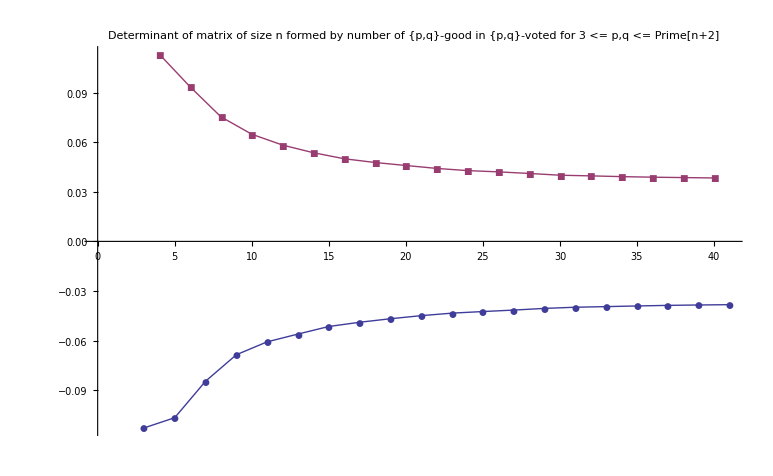

```mathematica
ListPlot[
{
Table[{mat[[i,1]],mat[[i,2]]},{i,1,Length[mat],2}],
Table[{mat[[i,1]],mat[[i,2]]},{i,2,Length[mat],2}]
}, Joined->True, PlotMarkers->Automatic, PlotLabel->"Determinant of matrix of size n formed by number of {p,q}-good in {p,q}-voted for 3 <= p,q <= Prime[n+2]"]
```

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
CloseStreams[]
```

Closing d:\triangle\Votes\3\139\GoodBadInVotedValues-3-139.txt

Closing d:\triangle\Votes\3\139\VotedValues.txt

```mathematica
-0.2418316830389526
```

```mathematica
eg=Table[
Eigenvalues[
Table[
Table[
If[PrimeQ[p]&&PrimeQ[q]&& p> 2 && q > 2 && p≠q,If[p<q,RatioFor[{p,q}],RatioFor[{q,p}]],0]
,{q,Prime[Range[2,range]]}
]
,{p,Prime[Range[2,range]]}

]
]
,{range,3,39}
]
```

{{-0.336009,0.336009},{0.775389,-0.452657,-0.322732},{1.32986,-0.565616,-0.446818,-0.317425},{1.93671,-0.620865,-0.558122,-0.443482,-0.31424},{2.61201,-0.685357,-0.619985,-0.552798,-0.441338,-0.312532},{3.31674,-0.71104,-0.685324,-0.619495,-0.549956,-0.439501,-0.311425},{4.06282,-0.752098,-0.711003,-0.684906,-0.618971,-0.547089,-0.437987,-0.31077},{4.85623,-0.797763,-0.751969,-0.710827,-0.684463,-0.618586,-0.545148,-0.437195,-0.310276},{5.66182,-0.812889,-0.792977,-0.751953,-0.710714,-0.684181,-0.618351,-0.543947,-0.436855,-0.309957},{6.49834,-0.84138,-0.809863,-0.792921,-0.751946,-0.710603,-0.683938,-0.618192,-0.54295,-0.436738,-0.309812},{7.35001,-0.861781,-0.832804,-0.809725,-0.792881,-0.751923,-0.710485,-0.683725,-0.618062,-0.542182,-0.436699,-0.309743},{8.20757,-0.87512,-0.845982,-0.832096,-0.809632,-0.792876,-0.751905,-0.710409,-0.683562,-0.617971,-0.541644,-0.436679,-0.309698},{9.07644,-0.891066,-0.853816,-0.845964,-0.832083,-0.809629,-0.792875,-0.751872,-0.710345,-0.683444,-0.617879,-0.541117,-0.436678,-0.309672},{9.96177,-0.907951,-0.868983,-0.85378,-0.845956,-0.832083,-0.809629,-0.792875,-0.751845,-0.7103,-0.683365,-0.617827,-0.540835,-0.436678,-0.309662},{10.8602,-0.925734,-0.88088,-0.868977,-0.853779,-0.845956,-0.832083,-0.809626,-0.792873,-0.751827,-0.710266,-0.68332,-0.617791,-0.540738,-0.436676,-0.309656},{11.7614,-0.940337,-0.887539,-0.880143,-0.868972,-0.853777,-0.845955,-0.832083,-0.809624,-0.792873,-0.751815,-0.71025,-0.683288,-0.617772,-0.540683,-0.436676,-0.309651},{12.6724,-0.956704,-0.89471,-0.887529,-0.880098,-0.868971,-0.853776,-0.845955,-0.832082,-0.809618,-0.792872,-0.751804,-0.710235,-0.68327,-0.617758,-0.540675,-0.436676,-0.309647},{13.5884,-0.97216,-0.900716,-0.894651,-0.887527,-0.880074,-0.86897,-0.853776,-0.845954,-0.832081,-0.809615,-0.792871,-0.751793,-0.710224,-0.683254,-0.617743,-0.540675,-0.436675,-0.309645},{14.506,-0.986077,-0.903713,-0.900714,-0.894623,-0.887525,-0.880064,-0.868969,-0.853776,-0.845954,-0.832079,-0.809612,-0.79287,-0.751787,-0.710218,-0.683245,-0.617736,-0.540675,-0.436675,-0.309644},{15.4308,-0.99985,-0.911455,-0.903516,-0.900552,-0.894615,-0.887522,-0.880057,-0.868968,-0.853775,-0.845954,-0.832079,-0.809609,-0.792869,-0.751783,-0.710215,-0.683229,-0.617728,-0.540666,-0.436675,-0.309643},{16.3594,-1.01323,-0.916345,-0.910539,-0.90346,-0.900504,-0.894605,-0.887519,-0.88005,-0.868966,-0.853775,-0.845954,-0.832078,-0.809606,-0.792868,-0.751779,-0.710213,-0.683219,-0.61772,-0.540647,-0.436675,-0.309643},{17.2938,-1.02646,-0.92267,-0.915059,-0.910426,-0.903443,-0.900482,-0.894599,-0.887519,-0.880043,-0.868964,-0.853775,-0.845954,-0.832076,-0.809604,-0.792868,-0.751776,-0.71021,-0.68321,-0.617716,-0.540608,-0.436675,-0.309641},{18.2352,-1.03965,-0.930304,-0.920859,-0.914944,-0.910408,-0.903438,-0.900466,-0.894596,-0.887519,-0.880038,-0.868962,-0.853774,-0.845954,-0.832075,-0.809603,-0.792867,-0.751774,-0.710207,-0.683199,-0.617714,-0.540541,-0.436675,-0.30963},{19.1789,-1.05267,-0.935309,-0.926023,-0.920666,-0.914906,-0.910396,-0.903435,-0.90046,-0.894594,-0.887518,-0.880033,-0.868961,-0.853774,-0.845954,-0.832075,-0.809601,-0.792867,-0.751773,-0.710205,-0.683193,-0.617712,-0.540467,-0.436675,-0.309612},{20.1223,-1.06614,-0.941681,-0.926608,-0.923158,-0.920661,-0.914897,-0.910395,-0.903432,-0.900454,-0.894593,-0.887518,-0.880031,-0.868959,-0.853774,-0.845953,-0.832074,-0.809599,-0.792866,-0.751771,-0.710203,-0.683187,-0.617711,-0.540392,-0.436675,-0.309599},{21.0685,-1.07827,-0.943983,-0.932123,-0.926376,-0.923148,-0.920632,-0.914885,-0.91039,-0.903431,-0.900449,-0.894589,-0.887518,-0.880025,-0.868959,-0.853773,-0.845953,-0.832074,-0.809598,-0.792866,-0.751771,-0.710201,-0.683181,-0.61771,-0.540306,-0.436674,-0.309569},{22.0145,-1.09082,-0.948323,-0.935774,-0.926439,-0.925562,-0.923126,-0.920609,-0.914879,-0.910387,-0.90343,-0.900448,-0.894589,-0.887517,-0.880023,-0.868958,-0.853773,-0.845953,-0.832073,-0.809597,-0.792866,-0.75177,-0.7102,-0.683177,-0.617709,-0.540235,-0.436673,-0.309546},{22.963,-1.10193,-0.950169,-0.936091,-0.935527,-0.926361,-0.925551,-0.923124,-0.920583,-0.914873,-0.910385,-0.903429,-0.900444,-0.894588,-0.887517,-0.880021,-0.868957,-0.853773,-0.845953,-0.832072,-0.809596,-0.792865,-0.751769,-0.710199,-0.683174,-0.617709,-0.540149,-0.436673,-0.309516},{23.9199,-1.11278,-0.953915,-0.942791,-0.935932,-0.935469,-0.926345,-0.925549,-0.923123,-0.92057,-0.914868,-0.910383,-0.903428,-0.90044,-0.894586,-0.887517,-0.880017,-0.868955,-0.853772,-0.845953,-0.832072,-0.809595,-0.792865,-0.751769,-0.710197,-0.683171,-0.617708,-0.540043,-0.436673,-0.309462},{24.8784,-1.12385,-0.957878,-0.944494,-0.941914,-0.935886,-0.935437,-0.926339,-0.925549,-0.923123,-0.920566,-0.914866,-0.910382,-0.903428,-0.900439,-0.894586,-0.887516,-0.880016,-0.868955,-0.853772,-0.845953,-0.832072,-0.809595,-0.792865,-0.751768,-0.710197,-0.683171,-0.617698,-0.539944,-0.436669,-0.309423},{25.839,-1.13491,-0.962302,-0.946075,-0.943755,-0.941909,-0.935869,-0.93543,-0.926337,-0.925547,-0.923122,-0.920564,-0.914865,-0.910381,-0.903428,-0.900439,-0.894586,-0.887516,-0.880016,-0.868955,-0.853772,-0.845953,-0.832072,-0.809595,-0.792865,-0.751768,-0.710196,-0.683171,-0.617681,-0.539828,-0.436661,-0.309383},{26.7987,-1.14716,-0.971805,-0.950975,-0.944309,-0.94191,-0.935874,-0.93543,-0.932712,-0.926337,-0.925547,-0.923122,-0.920563,-0.914865,-0.910381,-0.903428,-0.900439,-0.894586,-0.887516,-0.880016,-0.868955,-0.853772,-0.845952,-0.832071,-0.809594,-0.792865,-0.751768,-0.710196,-0.68317,-0.617665,-0.539734,-0.436653,-0.309341},{27.7634,-1.15794,-0.974098,-0.95369,-0.949305,-0.944176,-0.941898,-0.935871,-0.935421,-0.932711,-0.926336,-0.925547,-0.923122,-0.920562,-0.914865,-0.910381,-0.903428,-0.900439,-0.894586,-0.887516,-0.880016,-0.868955,-0.853772,-0.845952,-0.832071,-0.809593,-0.792864,-0.751768,-0.710194,-0.683165,-0.617621,-0.539618,-0.436635,-0.309295},{28.727,-1.17012,-0.981185,-0.963185,-0.950471,-0.944227,-0.941901,-0.935875,-0.935447,-0.933778,-0.932684,-0.926336,-0.925547,-0.923122,-0.920562,-0.914865,-0.910381,-0.903428,-0.900439,-0.894586,-0.887516,-0.880015,-0.868954,-0.853771,-0.845952,-0.83207,-0.809592,-0.792864,-0.751768,-0.710192,-0.683161,-0.617582,-0.539522,-0.436619,-0.309255},{29.6935,-1.18087,-0.982858,-0.963204,-0.954777,-0.950172,-0.944121,-0.941897,-0.935875,-0.93544,-0.933769,-0.932683,-0.926336,-0.925547,-0.923121,-0.920562,-0.914865,-0.91038,-0.903428,-0.900438,-0.894585,-0.887516,-0.880014,-0.868954,-0.853764,-0.845951,-0.832068,-0.809583,-0.792863,-0.751763,-0.710178,-0.683126,-0.617572,-0.539433,-0.436595,-0.30922},{30.6614,-1.19109,-0.984839,-0.963303,-0.958334,-0.952399,-0.950101,-0.944108,-0.941895,-0.935874,-0.935439,-0.933768,-0.932683,-0.926336,-0.925546,-0.923121,-0.920562,-0.914865,-0.91038,-0.903428,-0.900438,-0.894585,-0.887516,-0.880014,-0.868953,-0.853764,-0.845951,-0.832068,-0.809581,-0.792863,-0.751762,-0.710175,-0.683117,-0.617495,-0.539333,-0.436563,-0.309183},{31.6299,-1.20076,-0.987193,-0.963563,-0.960562,-0.954485,-0.952355,-0.95002,-0.944107,-0.941894,-0.935872,-0.935438,-0.933768,-0.932683,-0.926336,-0.925546,-0.923121,-0.920562,-0.914864,-0.910379,-0.903428,-0.900438,-0.894585,-0.887516,-0.880013,-0.868953,-0.853764,-0.845951,-0.832068,-0.809581,-0.792863,-0.751761,-0.710175,-0.683116,-0.617294,-0.539202,-0.436522,-0.309145}}

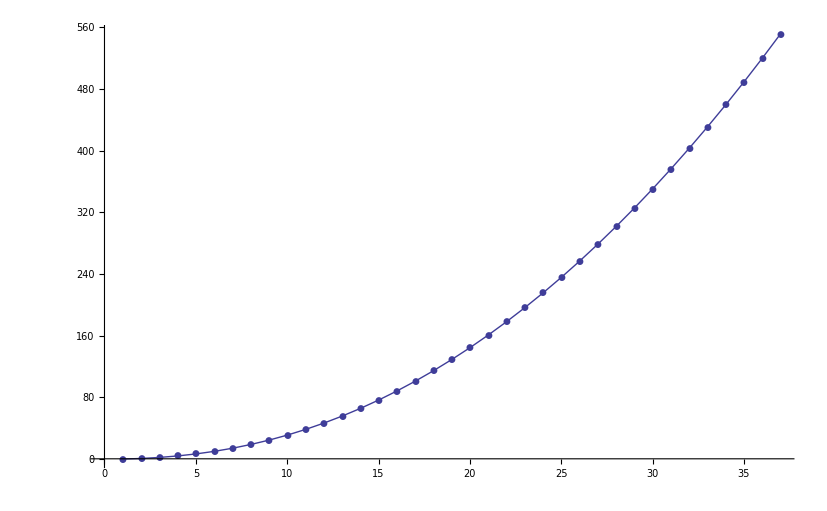

```mathematica
ListPlot[Accumulate[Map[#[[1]]&,eg]], Joined->True, PlotMarkers->Automatic]
```

```mathematica
ev=Table[
Eigenvectors[
Table[
Table[
If[PrimeQ[p]&&PrimeQ[q]&& p> 2 && q > 2 && p≠q,If[p<q,RatioFor[{p,q}],RatioFor[{q,p}]],0]
,{q,Prime[Range[2,range]]}
]
,{p,Prime[Range[2,range]]}

]
]
,{range,3,15}
]
```

{{{-0.707107,0.707107},{0.707107,0.707107}},{{-0.545042,-0.583794,-0.601759},{-0.163832,-0.629742,0.759332},{0.822246,-0.512455,-0.247591}},{{-0.444536,-0.491466,-0.516158,-0.542614},{-0.127625,-0.234015,-0.52022,0.811369},{-0.177042,-0.718869,0.647656,0.18007},{0.868767,-0.432349,-0.20855,-0.121759}},{{-0.379608,-0.42699,-0.453145,-0.479143,-0.488528},{-0.0507542,-0.0883652,-0.151983,-0.560682,0.807559},{-0.14432,-0.268981,-0.630428,0.650212,0.294288},{-0.181506,-0.767417,0.583206,0.153092,0.12067},{0.894175,-0.385477,-0.184371,-0.0992174,-0.0895664}},{{-0.333111,-0.378145,-0.404047,-0.430129,-0.438536,-0.453281},{-0.0560632,-0.0780845,-0.118323,-0.292692,-0.384906,0.861939},{0.052351,0.0895696,0.154317,0.614482,-0.76039,-0.0981924},{0.152106,0.282092,0.690683,-0.569793,-0.253788,-0.176555},{0.185065,0.796912,-0.541392,-0.139409,-0.105028,-0.08433},{0.908718,-0.358109,-0.169656,-0.087365,-0.0768264,-0.0605998}},{{-0.299153,-0.341391,-0.366957,-0.392158,-0.399962,-0.412657,-0.418639},{-0.0487304,-0.0623187,-0.110855,-0.212244,-0.2691,-0.257961,0.892999},{0.0575085,0.07985,0.121788,0.300437,0.395869,-0.852933,-0.0318582},{0.0529074,0.0891741,0.15617,0.640801,-0.737357,-0.0798887,-0.0644761},{-0.155124,-0.285251,-0.726135,0.526727,0.231883,0.147856,0.119266},{0.187063,0.817697,-0.510616,-0.128434,-0.0933712,-0.0695249,-0.0748611},{0.918134,-0.339477,-0.160727,-0.0796242,-0.0687053,-0.0509721,-0.0478938}},{{-0.272635,-0.311911,-0.336775,-0.361362,-0.368805,-0.380301,-0.385459,-0.393899},{-0.0407066,-0.0418362,-0.0743038,-0.154907,-0.19844,-0.248909,-0.216497,0.904915},{0.0494272,0.0627823,0.112078,0.215803,0.274495,0.268885,-0.886636,-0.0266988},{-0.0595796,-0.0811436,-0.125539,-0.314399,-0.41953,0.832964,0.0191239,0.0711342},{0.0527597,0.0869119,0.154358,0.663367,-0.717715,-0.0696079,-0.0515466,-0.0562436},{0.157404,0.284961,0.754782,-0.48959,-0.216085,-0.129393,-0.0976888,-0.107927},{0.189519,0.833594,-0.485108,-0.121003,-0.085813,-0.0602884,-0.0640981,-0.0642188},{-0.924415,0.326801,0.154556,0.0748875,0.0638759,0.0454482,0.0418592,0.0355585}},{{-0.251071,-0.287927,-0.311611,-0.335472,-0.342656,-0.353375,-0.357998,-0.365416,-0.374753},{-0.0431116,-0.0526473,-0.0699222,-0.13242,-0.166725,-0.212797,-0.210926,-0.119479,0.917115},{0.039135,0.0400134,0.0719426,0.149346,0.190645,0.236554,0.202983,-0.91298,0.0484742},{-0.0498817,-0.0631064,-0.112357,-0.218115,-0.279319,-0.285779,0.878475,0.015678,0.0409681},{0.061132,0.0826535,0.127835,0.324292,0.437923,-0.818049,-0.0168898,-0.0579526,-0.0574456},{-0.0527376,-0.0860126,-0.152676,-0.678463,0.704301,0.0643543,0.0449047,0.0469337,0.0423927},{0.159089,0.286347,0.773135,-0.464744,-0.205849,-0.118766,-0.0855567,-0.0928096,-0.080989},{0.190854,0.84344,-0.469524,-0.116228,-0.0812531,-0.0551342,-0.0581967,-0.057371,-0.0436121},{-0.928888,0.318005,0.14956,0.0712116,0.0602707,0.0415435,0.0376594,0.0308457,0.0295507}},{{-0.233839,-0.268709,-0.291076,-0.314166,-0.3211,-0.331211,-0.335437,-0.342116,-0.350367,-0.352937},{-0.0586159,-0.0752724,-0.0884532,-0.161303,-0.199955,-0.251242,-0.249849,-0.169772,0.323584,0.81117},{0.0178014,0.0197898,0.032856,0.0626456,0.0788751,0.0990575,0.0967317,0.0440505,-0.871288,0.455866},{-0.0387529,-0.0394934,-0.0715202,-0.1483,-0.189138,-0.233962,-0.200015,0.914995,-0.0429826,-0.0158002},{-0.0502956,-0.0636432,-0.11243,-0.219276,-0.281925,-0.295975,0.873762,0.00991112,0.0324385,0.0316915},{-0.0623537,-0.0841827,-0.129204,-0.330278,-0.44917,0.809003,0.0159438,0.0505743,0.047104,0.0444717},{-0.0529832,-0.0860681,-0.151622,-0.687607,0.696074,0.0612386,0.040978,0.0414756,0.0354922,0.032614},{0.160691,0.288747,0.784195,-0.449242,-0.199119,-0.112027,-0.0779398,-0.0834395,-0.0694609,-0.0629574},{0.191706,0.848852,-0.461177,-0.113464,-0.0786398,-0.0522633,-0.0549415,-0.053634,-0.0390653,-0.0283658},{-0.931809,0.312584,0.145903,0.0685708,0.0577098,0.0388312,0.0347583,0.027621,0.0257758,0.0236754}},{{-0.219446,-0.252484,-0.273454,-0.295897,-0.302572,-0.31221,-0.316129,-0.322269,-0.329685,-0.331969,-0.33771},{-0.0617365,-0.0779569,-0.0759751,-0.142845,-0.171697,-0.215623,-0.217147,-0.180326,0.00664537,0.117851,0.891268},{-0.042288,-0.0547818,-0.069967,-0.123592,-0.153818,-0.190459,-0.187659,-0.117017,0.322747,0.823407,-0.289883},{0.0173406,0.0192479,0.0329759,0.0622019,0.0783068,0.0977202,0.0950705,0.0415272,-0.880938,0.436654,0.0347866},{0.0389601,0.0397427,0.0715576,0.148681,0.189702,0.235202,0.201576,-0.913946,0.0450605,0.0181156,-0.00898318},{-0.0507426,-0.0641078,-0.112003,-0.219898,-0.283522,-0.304597,0.870097,0.00673852,0.0268871,0.0256028,0.0275443},{0.0635836,0.0855891,0.129766,0.334999,0.457853,-0.80195,-0.0162826,-0.0462149,-0.0404852,-0.0372254,-0.0372621},{-0.053393,-0.0863277,-0.150349,-0.69409,0.690265,0.0593376,0.0385671,0.0381835,0.0312376,0.0280719,0.0251989},{-0.162819,-0.291811,-0.791855,0.437473,0.193837,0.107169,0.0724962,0.0769027,0.0612945,0.0542726,0.054669},{-0.1925,-0.8516,0.45687,0.112151,0.0773448,0.0508891,0.0533821,0.05188,0.0369078,0.0260678,0.0160906},{0.933483,-0.309773,-0.143507,-0.0670068,-0.0561825,-0.0372675,-0.0330927,-0.0258034,-0.023651,-0.0214374,-0.0155184}},{{-0.20734,-0.238747,-0.258414,-0.280231,-0.28668,-0.295927,-0.299616,-0.305333,-0.312192,-0.314155,-0.319292,-0.322244},{-0.0726837,-0.0903627,-0.0799808,-0.150684,-0.179721,-0.225896,-0.230825,-0.204714,-0.0940944,0.00875389,0.379938,0.79098},{-0.0266158,-0.0344625,-0.0398463,-0.0714993,-0.0854122,-0.103909,-0.101328,-0.076016,0.0672064,0.106676,0.824431,-0.51155},{0.0414206,0.0537801,0.0699579,0.12281,0.152703,0.188234,0.184821,0.113329,-0.333788,-0.829112,0.26001,0.0567154},{0.0177435,0.0197031,0.032872,0.0625113,0.0787981,0.0989214,0.0966731,0.0437035,-0.876335,0.443372,0.0433803,-0.0252013},{-0.0392689,-0.0400899,-0.0715057,-0.149068,-0.190364,-0.236924,-0.203972,0.91253,-0.0465653,-0.0208744,0.00536258,0.014032},{0.051203,0.0645464,0.111418,0.220141,0.28467,0.312569,-0.86683,-0.00461631,-0.0234468,-0.0208718,-0.0214897,-0.0271603},{0.0647634,0.086899,0.130106,0.338799,0.465112,-0.795993,-0.0174176,-0.0432877,-0.036543,-0.0320126,-0.0306275,-0.033639},{-0.0538732,-0.0867057,-0.149225,-0.699155,0.685646,0.0579933,0.0369215,0.0358674,0.0285115,0.0248056,0.0212171,0.0221978},{-0.164944,-0.294841,-0.797282,0.428477,0.189857,0.103644,0.0686613,0.0722829,0.055927,0.0480353,0.0472481,0.0470767},{-0.193031,-0.85299,0.454675,0.111472,0.0766879,0.0502083,0.0526226,0.0510277,0.0359175,0.0249405,0.0147838,0.00924827},{0.934484,-0.308221,-0.141953,-0.0660208,-0.055235,-0.0363189,-0.0320952,-0.0247207,-0.0224429,-0.0201073,-0.0140171,-0.0106729}},{{-0.197027,-0.227012,-0.245565,-0.266757,-0.272995,-0.281906,-0.285391,-0.290764,-0.297105,-0.298897,-0.303565,-0.30632,-0.307573},{-0.0852995,-0.10554,-0.0918446,-0.169197,-0.200367,-0.250905,-0.255701,-0.231586,-0.121663,-0.039003,0.255538,0.484865,0.636938},{0.0115274,0.0146445,0.0145121,0.0284911,0.0340895,0.0411043,0.0427221,0.0351721,0.0241259,-0.0264967,-0.171586,-0.706611,0.680215},{0.0244218,0.031847,0.0383087,0.0683461,0.0814465,0.097834,0.0950473,0.069528,-0.0679104,-0.111098,-0.865122,0.406445,0.177731},{0.0407146,0.0529579,0.069714,0.121992,0.151602,0.186232,0.182568,0.11068,-0.336023,-0.834378,0.243909,0.0453681,0.0436035},{-0.0176248,-0.0195679,-0.0328944,-0.0624402,-0.0786827,-0.0985948,-0.096264,-0.0430983,0.877426,-0.441471,-0.0413512,0.027139,-0.00834344},{0.0395074,0.0403608,0.071459,0.149298,0.190779,0.238163,0.205641,-0.911524,0.0481598,0.0226663,-0.00289643,-0.0115188,-0.0125741},{0.051535,0.0648731,0.111028,0.220201,0.285286,0.317935,-0.864737,-0.00332666,-0.0207639,-0.0179519,-0.0177072,-0.0232561,-0.0214764},{0.0656808,0.0879316,0.130369,0.341492,0.470304,-0.791745,-0.018155,-0.0412507,-0.0332397,-0.0284021,-0.0259985,-0.0288744,-0.0290241},{0.0542753,0.087063,0.148484,0.702711,-0.682381,-0.057116,-0.0357598,-0.0342652,-0.0264122,-0.0225658,-0.0184823,-0.0193778,-0.0184624},{0.166608,0.297239,0.801136,-0.422087,-0.186946,-0.101169,-0.0658934,-0.0689927,-0.0517971,-0.0436369,-0.0420206,-0.0416857,-0.0392128},{-0.193383,-0.85385,0.453331,0.111037,0.0762685,0.0497861,0.0521451,0.0504962,0.0352652,0.0242452,0.0139795,0.00841921,0.00658649},{0.935187,-0.307166,-0.140843,-0.0653083,-0.0545525,-0.0356468,-0.0313829,-0.0239519,-0.0215527,-0.0191723,-0.012965,-0.00959039,-0.00861282}},{{-0.188056,-0.21679,-0.234279,-0.254937,-0.260998,-0.269587,-0.272907,-0.27801,-0.283925,-0.285584,-0.289867,-0.292381,-0.293506,-0.295576},{-0.0920343,-0.113856,-0.0931484,-0.174135,-0.206232,-0.254803,-0.260523,-0.243564,-0.149178,-0.0859592,0.139247,0.307711,0.414579,0.623956},{0.0245159,0.0302349,0.0352736,0.0573262,0.0661358,0.083844,0.0833691,0.0655307,0.0145504,-0.0356454,-0.212597,-0.364598,-0.522736,0.720029},{-0.0120346,-0.0152656,-0.0155414,-0.0299375,-0.0356892,-0.0431162,-0.0446504,-0.036381,-0.0238735,0.0286148,0.179963,0.722234,-0.659735,-0.0372377},{0.0243762,0.031788,0.0385533,0.0685039,0.0815507,0.097915,0.095042,0.0691915,-0.0685149,-0.112394,-0.869292,0.399603,0.170574,0.0196308},{-0.0406385,-0.0528632,-0.0697504,-0.121931,-0.151491,-0.186041,-0.182325,-0.110308,0.336358,0.834939,-0.242639,-0.0438551,-0.0418841,-0.00626293},{0.0175996,0.0195365,0.0329073,0.0624203,0.0786449,0.098522,0.0961692,0.0429473,-0.87756,0.441277,0.0410499,-0.0275185,0.00791649,0.00177155},{0.0397794,0.0406877,0.0712469,0.14952,0.1913,0.239533,0.207618,-0.910374,0.0495851,0.0242825,-0.000494319,-0.00860259,-0.00936126,-0.0162044},{-0.0518184,-0.0651773,-0.11052,-0.22025,-0.285953,-0.322213,0.863021,0.00267951,0.0188996,0.0159491,0.0150323,0.0201192,0.0180706,0.01922},{-0.0663849,-0.0887555,-0.130263,-0.343451,-0.474432,0.788496,0.0188311,0.0400411,0.031053,0.0260368,0.0228895,0.0252851,0.0251381,0.0241227},{-0.0546413,-0.0874258,-0.147447,-0.705949,0.679437,0.0562826,0.0347702,0.0329746,0.0246873,0.0207418,0.0162248,0.0168418,0.0157615,0.0182613},{0.168312,0.299936,0.804149,-0.416345,-0.184656,-0.0990207,-0.0635784,-0.0663463,-0.0484162,-0.0400477,-0.0377018,-0.0369039,-0.0341465,-0.038294},{0.193463,0.854023,-0.453055,-0.110958,-0.0761947,-0.0497062,-0.0520557,-0.0503995,-0.0351448,-0.0241172,-0.0138302,-0.00825626,-0.00641483,-0.00142393},{0.935653,-0.306533,-0.140009,-0.0648217,-0.0540998,-0.0351908,-0.0309041,-0.0234458,-0.020967,-0.0185603,-0.0122747,-0.00884981,-0.0078413,-0.00648032}}}

```mathematica
Map[Norm[#]&,ev]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

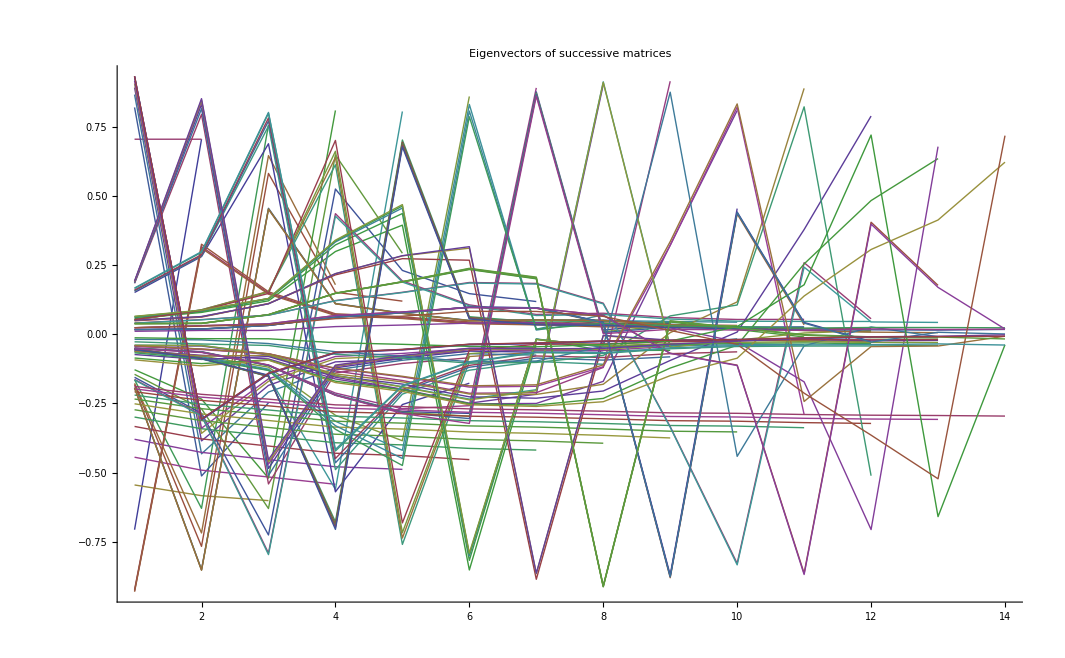

```mathematica
ListLinePlot[Sort[Flatten[ev,1]], PlotRange->All, PlotLabel->"Eigenvectors of successive matrices"]
```